```mathematica
L[p_]:=Log10[p];
a={-1,6.2218,-13.940,18.164,-9.2278,1.9923,-0.15643};
(* creates a polynomal function from whatever is stored in a *)
s[L_]:=L^Range[0,Length[a]-1].a;
c[θ_]:=Cos[θ];
b0={0.6639,-0.9587,0.2772};
b1={5.820,-6.864,1.367};
b2={10.39,-8.593,1.547};
z[c_,L_]:=L^Range[0,Length[b0]-1].b0+c*L^Range[0,Length[b1]-1].b1+c^2*L^Range[0,Length[b2]-1].b2;
cNorm=1;
rate[p_,θ_,ϕ_]:=cNorm*1/p^3*s[L[p]]*z[c[θ],L[p]]*1/(2*Pi)
(* For correctness checks: *)
s[L]
z[c,L]
rate[p,θ,ϕ]
```

-1+6.2218 L-13.94 L^2+18.164 L^3-9.2278 L^4+1.9923 L^5-0.15643 L^6

0.6639-0.9587 L+0.2772 L^2+c (5.82-6.864 L+1.367 L^2)+c^2 (10.39-8.593 L+1.547 L^2)

1/(2 p^3 π)(-1+2.70209 Log[p]-2.62925 Log[p]^2+1.48787 Log[p]^3-0.328273 Log[p]^4+0.0307805 Log[p]^5-0.00104961 Log[p]^6) (0.6639-0.416358 Log[p]+0.0522832 Log[p]^2+Cos[θ] (5.82-2.981 Log[p]+0.257832 Log[p]^2)+Cos[θ]^2 (10.39-3.73189 Log[p]+0.291782 Log[p]^2))

```mathematica
(* Integrate the formula *)
RateOverAllImpulse[θ_,ϕ_]:=∫_3^3000 rate[p,θ,ϕ]ⅆp
RateOverAllImpulse[θ,ϕ]
```

0.0184208-0.054097 Cos[θ]+0.0623457 Cos[(1.+0. ⅈ) θ]+0.0178896 Cos[(2.+0. ⅈ) θ]

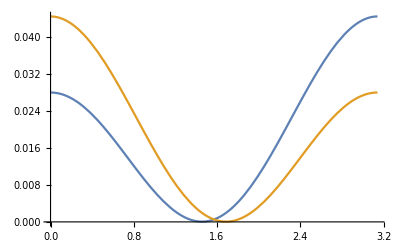

```mathematica
CopiedRate[θ_]:=0.018420759916164563-0.05409701020482868*Cos[θ]+0.062345742045134364*Cos[(1.+0.ⅈ) θ]+0.017889583588494178*Cos[(2.+0.ⅈ) θ]
CopiedRate2[θ_]:=0.018420759916164563-0.05409701020482868*Cos[θ]+0.062345742045134364*Cos[θ]+0.017889583588494178*Cos[2*θ]
Plot[{CopiedRate[Pi-x],CopiedRate2[x]},{x,0,Pi}]
```

```mathematica
L^Range[0,Length[a]-1].a
L^Range[0,Length[b0]-1].b0+c*L^Range[0,Length[b1]-1].b1+c^2*L^Range[0,Length[b2]-1].b2
```

-1+6.2218 L-13.94 L^2+18.164 L^3-9.2278 L^4+1.9923 L^5-0.15643 L^6

0.6639-0.9587 L+0.2772 L^2+c (5.82-6.864 L+1.367 L^2)+c^2 (10.39-8.593 L+1.547 L^2)

```mathematica
Array[10#&,10][[2]]
```

20

```mathematica
Length[b]
```

0